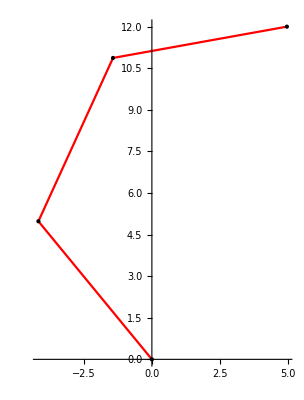

Tip : 10

X : 5

Y : 12

Base   : ( 0 , 0 )

Servo1 : ( -4.17812 , 4.97929 )

Servo2 : ( -1.4311 , 10.8703 )

Servo3 : ( 4.97015 , 11.999 )

```mathematica
tip = 10;y = 12; x = 5;
base=0;humerus = 6.5; ulna = 6.5; carpus = 6.5;
tipOnRad = tip Degree;
offsetX = Cos[tipOnRad] * carpus;
offsetY = Sin[tipOnRad] * carpus;
jointX = x - offsetX;
jointY =y -offsetY - base;
alpha1=ArcTan[jointX,jointY];
L = Sqrt[jointX^2+jointY^2];
sL = L^2;
sHumerus= humerus^2;
sUlna = ulna^2;
tHumerus = humerus*2;
al2num = sHumerus - sUlna + sL;
al2denum = tHumerus*L;
al2 = al2num / al2denum;
alpha2 = ArcCos[al2];
angle1 = (alpha1+alpha2)*180/Pi;
arm2num = sHumerus+sUlna-sL;
arm2denum = tHumerus*ulna;
arm2temp=ArcCos[arm2num/arm2denum];
angle2=arm2temp*180/Pi-180;
angle3=tip-angle1-angle2;
angle2=angle2+90;
angle3=angle3+90;
angle1=Round[angle1];
angle2=Round[angle2];
angle3=Round[angle3];

theta1 = angle1;theta2 = angle2-90;theta3 = angle3-90;
s1= Sin[theta1 Degree];s2 = Sin[theta1 Degree + theta2 Degree];s3 = Sin[theta1 Degree + theta2 Degree + theta3 Degree];
c1= Cos[theta1 Degree];c2 = Cos[theta1 Degree + theta2 Degree];c3 = Cos[theta1 Degree + theta2 Degree + theta3 Degree];
h1= s1*humerus; h2= s2*ulna;h3= s3*carpus;d1= c1*humerus; d2= c2*ulna;d3= c3*carpus;height = h1+h2+h3;depth = d1+d2+d3;
Print[
ListLinePlot[
{{0,base},{d1,h1},{d1+d2,h1+h2},{depth,height}},
PlotStyle->Red,  AspectRatio->Automatic,Mesh->All, MeshStyle->{Black,PointSize[Large]}]] 
Print["Tip : ",tip]
Print ["X : ",x]
Print ["Y : ",y]
Print["Base   : ( ", 0," , ",base," )"]
Print["Servo1 : ( ", d1," , ",h1," )"]
Print["Servo2 : ( ", d1+d2," , ",h1+h2," )"]
Print["Servo3 : ( ", depth," , ",height," )"]
```